```mathematica
k:=sqrt[2 m EE]/hbar
```

```mathematica
q:=sqrt[2 m (EE - V)]/hbar
```

```mathematica
Solve[-E^((2 I) d)==(k-I q Cot[a q])/(E^((2 I) a k) (k+I q Cot[a q])),d,MaxExtraConditions->Automatic]
```

{{d→ConditionalExpression[-1/2 ⅈ (2 ⅈ π C[1]+Log[(ⅇ^(-(2 ⅈ a sqrt[2 EE m])/hbar) (ⅈ sqrt[2 EE m]+Cot[(a sqrt[2 m (EE-V)])/hbar] sqrt[2 m (EE-V)]))/(-ⅈ sqrt[2 EE m]+Cot[(a sqrt[2 m (EE-V)])/hbar] sqrt[2 m (EE-V)])]),C[1]∈ℤ]}}

```mathematica
a = 1
```

1

```mathematica
m = 1
```

1

```mathematica
hbar = 1
```

```mathematica
1
V = 30
```

1

30

```mathematica
sol := Solve[-E^((2 I) d)==(k-I q Cot[a q])/(E^((2 I) a k) (k+I q Cot[a q])),d,MaxExtraConditions->Automatic]
```

```mathematica
Plot[Evaluate[d[EE]/.sol/.{C[1]-> 1}], {EE, 0.1, 100}, PlotRange->All]
```

-Graphics-

```mathematica
Solve[-E^((2 I) d)==(k-I q Cot[a q])/(E^((2 I) a k) (k+I q Cot[a q])),d,MaxExtraConditions->Automatic]
```

{{d→ConditionalExpression[-1/2 ⅈ (2 ⅈ π C[1]+Log[-(ⅇ^(-2 ⅈ sqrt[2 EE]) (-ⅈ Cot[sqrt[2 (-30+EE)]] sqrt[2 (-30+EE)]+sqrt[2 EE]))/(ⅈ Cot[sqrt[2 (-30+EE)]] sqrt[2 (-30+EE)]+sqrt[2 EE])]),C[1]∈ℤ]}}

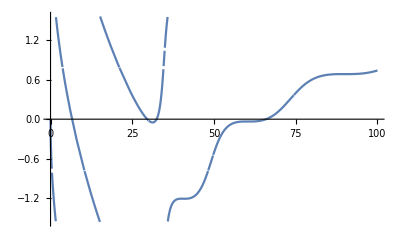

```mathematica
Plot[d,{EE,0,100}]
```

```mathematica
D[d,EE]
```

(ⅈ ⅇ^(2 ⅈ √2 √EE) (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) ((ⅈ √2 ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))/(√EE (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))+(ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) (1/(√2 √EE)+(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))-ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])^2-(ⅇ^(-2 ⅈ √2 √EE) (1/(√2 √EE)-(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))+ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])))/(2 (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))

```mathematica
derFunction[EE_]:=D[d,EE]
```

```mathematica
phase[EE_]:=-1/2 ⅈ (Log[-(ⅇ^(-2 ⅈ Sqrt[2 EE]) (-ⅈ Cot[Sqrt[2 (-30+EE)]] Sqrt[2 (-30+EE)]+Sqrt[2 EE]))/(ⅈ Cot[Sqrt[2 (-30+EE)]] Sqrt[2 (-30+EE)]+Sqrt[2 EE])])
```

```mathematica
phase[EE]
```

-1/2 ⅈ Log[-(ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])]

```mathematica
D[phase[EE],EE]
```

(ⅈ ⅇ^(2 ⅈ √2 √EE) (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) ((ⅈ √2 ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))/(√EE (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))+(ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) (1/(√2 √EE)+(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))-ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])^2-(ⅇ^(-2 ⅈ √2 √EE) (1/(√2 √EE)-(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))+ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])))/(2 (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))

```mathematica
dffPhase[EE_]:= (ⅈ ⅇ^(2 ⅈ √2 √EE) (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) ((ⅈ √2 ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))/(√EE (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))+(ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) (1/(√2 √EE)+(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))-ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])^2-(ⅇ^(-2 ⅈ √2 √EE) (1/(√2 √EE)-(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))+ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])))/(2 (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))
```

```mathematica
N[dffPhase[1]]
```

-0.614259+0. ⅈ

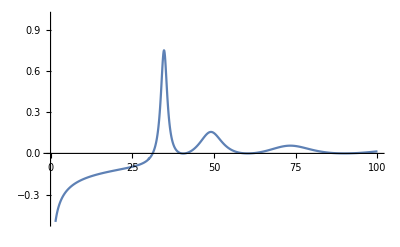

```mathematica
ListLinePlot[Table[{x, N[dffPhase[eng]]/.eng ->x},{x,0.1,100,0.1}],PlotRange-> {-0.5,1}]
```

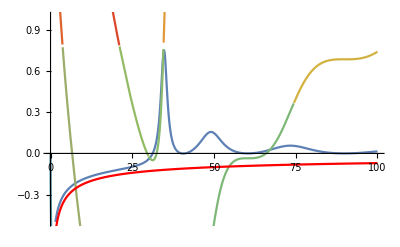

```mathematica
Show[ListLinePlot[Table[{x, N[dffPhase[eng]]/.eng ->x},{x,0.1,100,0.1}],PlotRange-> {-0.5,1}],Plot[d,{EE,0,100},ColorFunction->"Rainbow"],Plot[-1/(Sqrt[2EE]),{EE,0,100},ColorFunction->Hue,PlotRange->All]]
```